## 0th order approximation for the energy of the macro impact dissapated as heat.

Using the equation: E_tot = L*m = L*ρ*π*h*r^2, and solving for r, we find the a Macro of a given energy could melt a cylinder of the following radius (with height h equal to the diameter of the impacted body).
Note that this ignores the energy required to heat a cylinder of these dimensions to the melting point (which, for rock on the moon, may be considerable).

```mathematica
rMelt[eTot_,L_,ρ_,h_]=Sqrt[eTot/(L*ρ*π*h)];
```

For steel-like parameters, with diameter of earth:

```mathematica
rMelt[4.5*10^12,2.5*10^5,7850,1.2*10^7]
```

0.00779895

For rock-like parameters,  with diameter of earth

```mathematica
rMelt[4.5*10^12,300,2500,1.2*10^7]
```

0.398942

```mathematica
rMelt[eTot_,L_,ρ_,h_]=Sqrt[eTot/(L*ρ*π*h)];
```

To account for the energy cost to heat the cylinder, we include the term c*m*(Temp_final - Temp_initial).  Even if this energy will be transformed to seismic wave, it still should be accounted for in computing the melt radius.

Assume the initial temperature of the rock is around 300 K.

```mathematica
rMeltWithHeating[eTot_,L_,ρ_,h_,c_,TempInitial_,TempFinal_]=Sqrt[eTot/((L+c(TempFinal-TempInitial))(ρ*π*h))];
```

```mathematica
rMeltWithHeating[4.5*10^12,2.5*10^5,7850,1.2*10^7, 500,300,1800]
```

0.00389947

```mathematica
rMeltWithHeating[4.5*10^12,500,2500,1.2*10^7, 1000,300,1500]
```

0.00630652

```mathematica
energyDissapatedApprox[L_,ρ_,h_,rMacro_]=L*(ρ*π*h)*rMacro^2;
```

```mathematica
energyDissapatedApprox[10^5,2500,1.2*10^7,0.006306517584052074]
```

3.74844×10^11

## 1st order approximation for dissipated energy

### Energy required to sublimate (turn a solid directly into vapor) impacted material:

As attempt to establish a lower bound for the energy that is unequivocally dissipated that relies on fewer parameters of the impacted material, consider the energy required to vaporize a cylinder of material (with parameters akin to rock) with radius equal to the macro and length h equal to the diameter of the moon, which is given by

```mathematica
energyDissapatedApproxIncludingVaporization[Lmelt_,Lvaporize_,ρ_,h_,rMacro_]=(Lmelt+Lvaporize)*(ρ*π*h)*rMacro^2;
```

```mathematica
energyDissapatedApproxIncludingVaporization[300,4000,2500,2*1.7*10^6,10^-6]
```

114.825

## 2nd order approximation to plastic work/dissipated energy

### Using the model of “Hypervelocity penetration modeling- momentum vs. energy and energy transfer mechanisms” by Walker to compute the plastic work done by the Macro

As noted, for cavity expasion velocities vcavity ≥ 0.2vsound the elastic-plastic interface velocity is nearly the bulk sound speed: vplastic ≈ vsound.  Note that y is the yield strength of the impacted material, r is the (final) cavity radius, and vcavity is the cavity expansion velocity.  The following assumes that r ≈ r_macro, 
and that vcavity ≈ v_macro.

```mathematica
plasticWork[r_,y_,vcavity_,vplastic_]=π*r^2*y((2/Sqrt[1-(vcavity/vplastic)^2])Log[Sqrt[1-(vcavity/vplastic)^2]/(vcavity/vplastic)+1/(vcavity/vplastic)]-1);
```

In the limit of v -> infinity, the plastic work becomes negative in this model, which also happens with v = 2.5*10^6.  Hence, this model clearly does not work for the macro case.

```mathematica
Module[{vplastic= 1000},Limit[plasticWork[r_,y_,vcavity_,vplastic_],vcavity-> Infinity]]
```

-π r^2 y

```mathematica
Chop[plasticWork[10^-6,10^9,2.5*10^6,1000],10^-9]
```

-0.00313765

```mathematica
Manipulate[Plot[plasticWork[r,y,vcavity,vplastic],{vplastic,1000,8000}],{y,10^7,10^9},{r,10^-11,10^-5},{vcavity,10^4,10^6}]
```

## 1st order approximation to dynamics of energy deposition

This model uses a delta potential initial condition for the heat equation in cylindrical coordinates to model the macro’s energy being converted to heat.  This model views the impact as an instantaneous input of heat along the z-axis.

This model/initial condition is reasonable given that the delta source becomes a Gaussian with the same energy an instant after the initial input of the delta source (assuming energy is conserved at least in the intial instant).

Note that c1 = a =λ/(ρ c), where λ,ρ and c are the thermal conductivity, density and heat capacity of the material respectively.  The first equation below is the inverse Hankel transform of the solution to the heat equation in k-space:

```mathematica
Assumptions[t>0&&c1>0&&rx>0&&r>0,c2*Integrate[k Exp[-c1*k^2*t]*BesselJ[0,k*r],{k,0,Infinity}]]
```

Assumptions[t>0&&c1>0&&rx>0&&r>0,ConditionalExpression[(c2 ⅇ^(-r^2/(4 c1 t)))/(2 c1 t),Re[r]≥0&&Re[c1 t]≥0&&(Re[r]>0||Im[r]>0)]]

Solving for r_melt by setting the above (after applying initial conditions -- the FT of the delta function intial condition gives c2 = (2π rx Q)/(c ρ σ) , see the LATEX documnet for detials) equal to melt temperature Θ, gives r_melt = 4 a t*Log[(rx Q)/(4 a c π t Θ ρ σ)] and then differentiating w.r.t to time gives r_dot_met:

```mathematica
D[Sqrt[4 a t*Log[(rx Q)/(2 a c t Θ ρ σ)]],t]
```

(-a+a Log[(Q rx)/(2 a c t Θ ρ σ)])/(√(a t Log[(Q rx)/(2 a c t Θ ρ σ)]))

Since a Log[(Q rx)/(2 a c t Θ ρ σ)] is on the order of 10 for the given parameters, it is >> 1, and so we can drop the -1 term and proceed as follows:

```mathematica
Solve[(a Log[(rx Q)/(2a c  t Θ ρ σ)])/t==vs^2,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(a ProductLog[(Q rx vs^2)/(2 a^2 c Θ ρ σ)])/vs^2}}

So the time elapsed until the melt wave velocity drops to the speed of sound is (using a macro radius of first 10^-11 and then 10^-6):

```mathematica
N[(a ProductLog[(Q rx vs^2)/(2 a^2 c Θ ρ σ)])/vs^2]/.{a->10^-6,c->10^3,Θ->10^3,Q-> 10^5,ρ->10^3,σ->10^-11,vs-> 10^3,rx-> 10^-11}
```

2.82036×10^-11

```mathematica
N[(a ProductLog[(Q rx vs^2)/(2 a^2 c Θ ρ σ)])/vs^2]/.{a->10^-6,c->10^3,Θ->10^3,Q-> 10^5,ρ->10^3,σ->10^-11,vs-> 10^3,rx-> 10^-6}
```

3.93826×10^-11

Notice that for 10^-6 ≤ r ≤ 10^-11, t << 10^(-3.5) so the approximation of dropping the -1 term is valid.

```mathematica
Assuming[{Q,t,a,rx,c,θ,ρ,σ,vs}∈Reals,FullSimplify[Sqrt[4 a t*Log[(rx Q)/(4 a c π t Θ ρ σ)]]/.t->(a ProductLog[(Q rx vs^2)/(2 a^2 c Θ ρ σ)])/vs^2]]
```

2 √((a^2 Log[(ⅇ^ProductLog[(Q rx vs^2)/(2 a^2 c Θ ρ σ)])/(2 π)] ProductLog[(Q rx vs^2)/(2 a^2 c Θ ρ σ)])/vs^2)

This actually simplifies further by the identity W[x] = ln[x/W[x]], which gives r_melt_fast = 2 a/vs  ProductLog[(Q rx vs^2)/(2 a^2 c π Θ ρ σ)] = 2 a/vs  ProductLog[(rx  vx^2 vs^2)/(2 a^2 c π Θ)].

This expression for $r_\te{fast melt}$ is highly sensitive to $\alpha$ and $v_p$ and relatively insensitive to the macro’s parameters.

It gives results on the order of micrometers to tenths of micrometers for most marco radii which, for $r_X > 10^-8$ results in $r_\te{fast melt} < r_X$ which is a bit of a problem.

```mathematica
N[2 a/vs  ProductLog[(Q rx vs^2)/(2 a^2 c π Θ ρ σ)]]/.{a->10^-6,c->10^3,Θ->10^3,Q-> 10^5,ρ->10^3,σ->10^-11,vs-> 10^3,rx-> 10^-11}
```

5.41976×10^-8

```mathematica
N[2 a/vs  ProductLog[(Q rx vs^2)/(2 a^2 c π Θ ρ σ)]]/.{a->10^-6,c->10^3,Θ->10^3,Q-> 10^5,ρ->10^3,σ->10^-11,vs-> 10^3,rx-> 10^-6}
```

7.65333×10^-8

Below is a plot of r_melt_fast, and the x-axis is in terms of the of macro radius.

```mathematica
Manipulate[Plot[2 a/vs  ProductLog[(rx  vx^2 vs^2)/(2 a^2 c π Θ)],{rx,0,10^-6}],{a,10^-7,10^-4},{c,10^2,10^3},{Θ,10^3,2.5*10^3},{Q,10^4,10^7},{ρ,10^3,10^4},{σ,10^-11,10^-7},{vs,10^3,10^4},{rx, 10^-11,10^-5},{vx,10^4,10^6}]
```

These results imply that either much of the melting occurs once the temperature field’s expansion is slower than the speed of sound and this slow-down occurs very quickly (as shown above within the assumptions of the model), or that the material parameters -- especially $\alpha$ and $c_p$ -- are far from constant (or may not even be well defined) in our case. 

As an interesting note, the values found in this model for both the time of the melt wave to fall to the speed of sound and the radius of the quickly melted material are within 1 order of magnitude of those found using a corrected form of “Localization of strain and the melting wave in high-speed penetration” as shown below.

## 2nd order approximation to dynamics of energy deposition

### Using (a corrected form of) the melt zone model in “Localization of strain and the melting wave in high-speed penetration” by Stepanenko and Slepyan:

First ploting and then solving (numerically) for the parameter Y that determines the “best fit model with a Sqrt[t] functional form” of the melt wave:

```mathematica
Manipulate[Plot[Re[{-(v0^2*μ Erfi[√(y ((c μ)/λ-2))])/(λ √(π ((c μ)/λ-2)) Erf[√y]^2)+(√((c μ)/λ)Θ)/(√π  Erfc[√((c y μ)/λ)])-√y ⅇ^((c y μ)/λ) L}],{y,0,10},PlotRange-> {-1,1}],{v0,1,2.5*10^6},{μ,10^-1,10^9},{λ,5,50},{c,500,1000},{L,500,2.5*10^5},{Θ,1500,1800}]
```

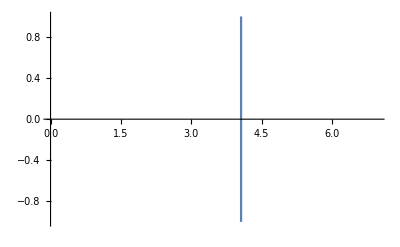

```mathematica
Module[{v0=2.5*10^6,
μ=0.5,
λ=5,
c=1000,
L= 500,Θ=1500,ρ=2500},Plot[Re[-(v0^2*μ Erfi[√(y ((c μ)/λ-2))])/(λ √(π ((c μ)/λ-2)) Erf[√y]^2)+(√((c μ)/λ)Θ)/(√π  Erfc[√((c y μ)/λ)])-√y ⅇ^((c y μ)/λ) L],{y,0,10},PlotRange-> {-1,1}]]
```

```mathematica
Module[{v0=2.5*10^6,
μ=0.5,
λ=5,
c=1000,
L= 500,Θ=1500,ρ=2500},NSolve[-(v0^2*μ Erfi[√(y ((c μ)/λ-2))])/(λ √(π ((c μ)/λ-2)) Erf[√y]^2)+(√((c μ)/λ)Θ)/(√π  Erfc[√((c y μ)/λ)])-√y ⅇ^((c y μ)/λ) L==0&&4<y≤5,y]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y→4.06172}}

The above gives us the melt wave as a function of time:

```mathematica
X[y_,t_]=2Sqrt[μ*y*t/ρ];
```

```mathematica
X[4.06172405151474,t]
```

0.0570033 √t

Now, we solve for the time at which the melt wave velocity falls to the speed of sound:

```mathematica
D[X[4.06172405151474,t],t]
```

0.0285017/(√t)

```mathematica
timeVelocityFallsToSpeedOfSound=Solve[0.028501663290112528/(√t)==8000,t]
```

{{t→1.26929×10^-11}}

```mathematica
radiusOfFasterThanSoundMaterial=Solve[X[4.06172405151474,timeVelocityFallsToSpeedOfSound[[1,1,2]]]==r,r]
```

{{r→2.03086×10^-7}}

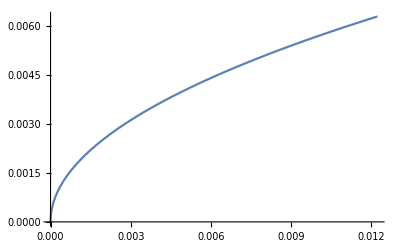

```mathematica
Plot[X[4.06172405151474,t],{t,0,0.012239926793871484}]
```

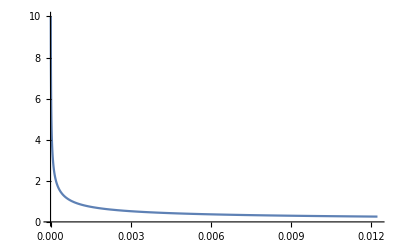

```mathematica
Plot[0.028501663290112528/(√t),{t,0,0.012239926793871484},PlotRange-> {0,10}]
```

Solving for a rough estimate of the total time taken by the melt wave to reach its full extent using the value of rMeltWithHeating for rock parameters found in section above:

```mathematica
Solve[0.057003326580225055 √t==0.006306517584052074,t]
```

{{t→0.0122399}}

## Conclusions

Two models that attempted to capture the macro impact’s dynamics appear to imply that either much of the melting occurs once the temperature field’s expansion is slower than the speed of sound and this slow-down occurs very quickly (as shown above within the assumptions of the model), or that the material parameters of the impacted material -- especially $\alpha$ and $c_p$ -- are far from constant (or may not even be well defined) in our case. 

As noted above, the values found in both models for the time of the melt wave to fall to the speed of sound and the radius of the quickly melted material are within 1 order of magnitude of each other.  It is worth noting that the assumptions of both models -- that the energy deposition of the macro is immediately turned to either heat as an initial condition or through the creation of plastic shear strain which is immediately turned to heat -- will tend to de-emphasize the significance of the parameters of the macro, and (over)emphasize the significance of the parameters of the impacted material. 

A model that would best reflect the physics of macro impacts should:
1. be sensitive to the macro’s parameters
2. be relatively insensitive to the impacted material’s parameters (unless macro-macro collisions are to be considered).
3. Take into account the effects of QM when the macro radii considered are on atomic scales.
4. Take into account the effects of SR when the macro speeds achieve an appreciable fraction of c.

Given the speeds (fast), densities (large) and sizes (small) involved in macro impacts it is possible that these dynamics can’t be well modeled by purely classical means -- macros might represent an interesting semi-classical limit of general-relativistic quantum mechanics.